# Bessel Functions

Separation of variables on circular/annular domains produces Bessel functions that satisfy the ODE
	x^2 y''+x y'+(x^2-α^2)y=0
for different constants α.  A Power Series obtained by substituting the Frobenius expansion
	y=∑_(k=0)^∞ a_k z^(k+r)
into the ODE and equating coefficients gives the definition
	J_α(x)=∑_m (-1)^m/(m! Γ(m+α+1))(X/2)^(2 m+α)
for solution that are non singular at x=0.
https://en.wikipedia.org/wiki/Frobenius_method
https://en.wikipedia.org/wiki/Bessel_function

## Bessel Plots

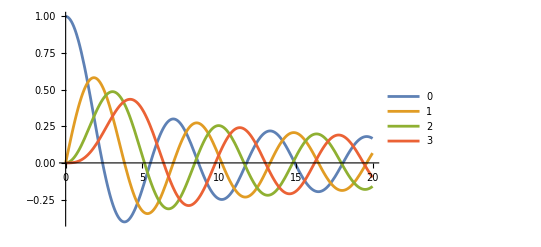

```mathematica
Plot[ {BesselJ[0,x],BesselJ[1,x],BesselJ[2,x],BesselJ[3,x]},{x,0,20},
PlotLegends->Range[0,3]]
```

Zeros for these functions are also standard computational fare.

```mathematica
Hmm=Table[BesselJZero[i,j],{i,0,3},{j,1,5}]
TraditionalForm[Hmm];
TableForm[N[Hmm],TableHeadings->{{Subscript[J, 0],Subscript[J, 1],Subscript[J, 2],Subscript[J, 3]},Automatic}];
```

{{BesselJZero[0,1],BesselJZero[0,2],BesselJZero[0,3],BesselJZero[0,4]},{BesselJZero[1,1],BesselJZero[1,2],BesselJZero[1,3],BesselJZero[1,4]},{BesselJZero[2,1],BesselJZero[2,2],BesselJZero[2,3],BesselJZero[2,4]},{BesselJZero[3,1],BesselJZero[3,2],BesselJZero[3,3],BesselJZero[3,4]}}

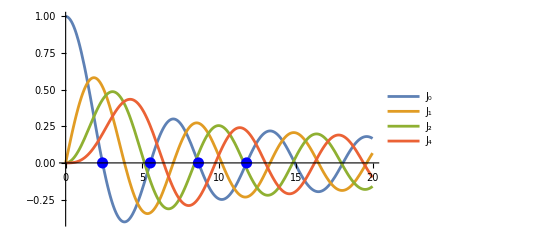

```mathematica
Plot[ {BesselJ[0,x],BesselJ[1,x],BesselJ[2,x],BesselJ[3,x]},{x,0,20},
PlotLegends->{Subscript[J, 0],Subscript[J, 1],Subscript[J, 2],Subscript[J, 4]},
Epilog->{PointSize[0.02],
{Blue, Table[Point[{BesselJZero[0,j],0}],{j,1,4}]}
}]
```

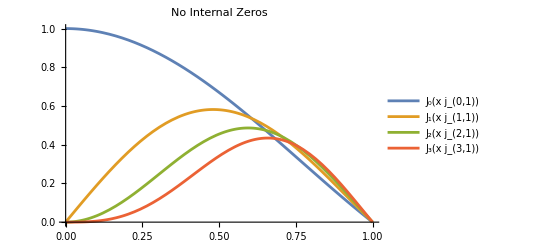

```mathematica
Plot[ {
BesselJ[0,BesselJZero[0,1]x],
BesselJ[1,BesselJZero[1,1]x],
BesselJ[2,BesselJZero[2,1]x],
BesselJ[3,BesselJZero[3,1]x]
},{x,0,1},
PlotLabel->"No Internal Zeros",
PlotLegends->Table[Subscript[J, i][Subscript[j, i,1] x],{i,0,3}]]
```

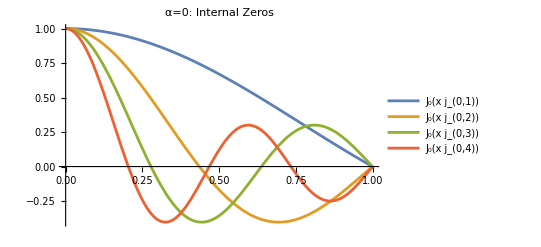

```mathematica
Plot[ {
BesselJ[0,BesselJZero[0,1]x],
BesselJ[0,BesselJZero[0,2]x],
BesselJ[0,BesselJZero[0,3]x],
BesselJ[0,BesselJZero[0,4]x]
},{x,0,1},
PlotLabel->"α=0: Internal Zeros",
PlotLegends->Table[Subscript[J, 0][Subscript[j, 0,i] x],{i,1,4}]]
```

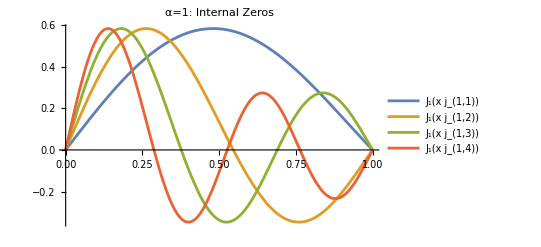

```mathematica
Plot[ {
BesselJ[1,BesselJZero[1,1]x],
BesselJ[1,BesselJZero[1,2]x],
BesselJ[1,BesselJZero[1,3]x],
BesselJ[1,BesselJZero[1,4]x]
},{x,0,1},
PlotLabel->"α=1: Internal Zeros",
PlotLegends->Table[Subscript[J, 1][Subscript[j, 1,i] x],{i,1,4}]]
```

## Mode Plots

In our new notation the cosine eigenmodes for the drum head are
	u_(i,k)= cos(i θ)J_i(r j_(i,k))

```mathematica
Do[
j[i,k]=N[BesselJZero[i,k]],
{i,0,3},{k,1,3}];
u[i_,k_][r_,θ_]:=Cos[ i θ] BesselJ[i,r j[i,k]]
TableForm[Table[
ParametricPlot3D[ {r Cos[θ], r Sin[θ], u[i,k][r,θ] },
{θ,0, 2π},{r,0,1}],
{i, 0, 3},
{k,1,3}],
TableHeadings->{Range[0,3],Range[1,3]}]
```

| 1 | 2 | 3
0 | -Graphics3D- | -Graphics3D- | -Graphics3D-
1 | -Graphics3D- | -Graphics3D- | -Graphics3D-
2 | -Graphics3D- | -Graphics3D- | -Graphics3D-
3 | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
Contr
```

```mathematica
Plot[ {BesselJ[0,x],BesselJ[1,x],BesselJ[2,x],BesselJ[3,x]},{x,0,20},
PlotLegends->Range[0,3]]
```

-Graphics-

Zeros for these functions are also standard computational fare.

```mathematica
Hmm=Table[BesselJZero[i,j],{i,0,3},{j,1,4}]
TraditionalForm[Hmm];
TableForm[N[Hmm],TableHeadings->{{Subscript[J, 0],Subscript[J, 1],Subscript[J, 2],Subscript[J, 4]},Automatic}];
```

{{BesselJZero[0,1],BesselJZero[0,2],BesselJZero[0,3],BesselJZero[0,4]},{BesselJZero[1,1],BesselJZero[1,2],BesselJZero[1,3],BesselJZero[1,4]},{BesselJZero[2,1],BesselJZero[2,2],BesselJZero[2,3],BesselJZero[2,4]},{BesselJZero[3,1],BesselJZero[3,2],BesselJZero[3,3],BesselJZero[3,4]}}

```mathematica
Plot[ {BesselJ[0,x],BesselJ[1,x],BesselJ[2,x],BesselJ[3,x]},{x,0,20},
PlotLegends->{Subscript[J, 0],Subscript[J, 1],Subscript[J, 2],Subscript[J, 4]},
Epilog->{PointSize[0.02],
{Blue, Table[Point[{BesselJZero[0,j],0}],{j,1,4}]}
}]
```

-Graphics-

```mathematica
Plot[ {
BesselJ[0,BesselJZero[0,1]x],
BesselJ[1,BesselJZero[1,1]x],
BesselJ[2,BesselJZero[2,1]x],
BesselJ[3,BesselJZero[3,1]x]
},{x,0,1},
PlotLabel->"No Internal Zeros",
PlotLegends->Table[Subscript[J, i][Subscript[j, i,1] x],{i,0,3}]]
```

-Graphics-

```mathematica
Plot[ {
BesselJ[0,BesselJZero[0,1]x],
BesselJ[0,BesselJZero[0,2]x],
BesselJ[0,BesselJZero[0,3]x],
BesselJ[0,BesselJZero[0,4]x]
},{x,0,1},
PlotLabel->"α=0: Internal Zeros",
PlotLegends->Table[Subscript[J, 0][Subscript[j, 0,i] x],{i,1,4}]]
```

-Graphics-

```mathematica
Plot[ {
BesselJ[1,BesselJZero[1,1]x],
BesselJ[1,BesselJZero[1,2]x],
BesselJ[1,BesselJZero[1,3]x],
BesselJ[1,BesselJZero[1,4]x]
},{x,0,1},
PlotLabel->"α=1: Internal Zeros",
PlotLegends->Table[Subscript[J, 1][Subscript[j, 1,i] x],{i,1,4}]]
```

-Graphics-